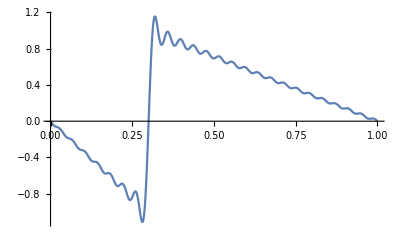

```mathematica
f[a_,L_,L1_,N_,x_]:=∑_(k=1)^N ((4×a)/(k×π)×Cos[(k×π×L1)/L]+(2×a×L)/(k×π)^2×(1/(L-L1)-1/L1)×Sin[(k×π×L1)/L])×(Sin[(k×π×x)/L]);
Plot[f[1,1,0.3,50,x],{x,0,1}]
```

```mathematica
b=Table[x,{x,0,1,0.001}];
a1=Table[f[1,1,0.04,50,x],{x,0,1,0.001}]
```

{0.,-0.0207348,-0.0418259,-0.0636167,-0.0864251,-0.110532,-0.13617,-0.163513,-0.192669,-0.223671,-0.256476,-0.290958,-0.326907,-0.364034,-0.401969,-0.44027,-0.478426,-0.515872,-0.55199,-0.58613,-0.617618,-0.645769,-0.669906,-0.689367,-0.703528,-0.71181,-0.713697,-0.708746,-0.696599,-0.676992,-0.649765,-0.614865,-0.572352,-0.5224,-0.465296,-0.40144,-0.331336,-0.255589,-0.174893,-0.0900226,-0.00181893,0.0888228,0.180969,0.273662,0.365937,0.456839,0.545437,0.630841,0.712216,0.788795,0.859894,0.92492,0.983381,1.03489,1.07919,1.1161,1.14561,1.16778,1.1828,1.19096,1.19267,1.18839,1.17868,1.16417,1.14553,1.12348,1.09876,1.07211,1.04428,1.01599,0.987935,0.960766,0.935078,0.911397,0.890183,0.87181,0.856574,0.844681,0.83625,0.831314,0.829823,0.831645,0.836578,0.844352,0.85464,0.867069,0.881225,0.896671,0.912952,0.929609,0.946191,0.962263,0.977414,0.991272,1.00351,1.01383,1.02203,1.02793,1.03142,1.03246,1.03107,1.02731,1.02133,1.0133,1.00345,0.992049,0.979389,0.965792,0.951596,0.937142,0.922772,0.908814,0.895582,0.883364,0.872415,0.862955,0.855161,0.849165,0.845053,0.842862,0.842581,0.844151,0.84747,0.852394,0.858742,0.866301,0.874835,0.884084,0.893779,0.903642,0.913399,0.922782,0.931537,0.939431,0.946255,0.951832,0.956019,0.958708,0.959832,0.959364,0.957314,0.953736,0.948716,0.942378,0.934876,0.926389,0.917119,0.907283,0.897112,0.886837,0.87669,0.866899,0.857676,0.849217,0.841697,0.835263,0.830036,0.826101,0.823514,0.822294,0.822426,0.823863,0.826523,0.830299,0.835054,0.840631,0.846853,0.853529,0.860461,0.867447,0.874283,0.880777,0.886742,0.892012,0.896436,0.899888,0.902269,0.903505,0.903554,0.902402,0.900067,0.896596,0.892062,0.886565,0.880229,0.873194,0.865621,0.857677,0.84954,0.841389,0.833403,0.825754,0.818602,0.812096,0.806366,0.801519,0.797642,0.794796,0.793014,0.792303,0.792645,0.793993,0.796277,0.799405,0.803263,0.80772,0.812635,0.817852,0.823212,0.828553,0.833717,0.838548,0.842904,0.846654,0.849684,0.851899,0.853225,0.853612,0.853032,0.851484,0.848988,0.845591,0.841359,0.83638,0.83076,0.824619,0.818089,0.811311,0.804432,0.797598,0.790953,0.784637,0.778779,0.773494,0.768885,0.765035,0.762008,0.759846,0.75857,0.758178,0.758647,0.759932,0.761967,0.764669,0.76794,0.771665,0.775723,0.779983,0.78431,0.788569,0.792629,0.796362,0.799653,0.802396,0.8045,0.805893,0.806517,0.806339,0.805341,0.80353,0.800931,0.797589,0.793567,0.788945,0.783817,0.778289,0.772477,0.766502,0.76049,0.754564,0.748846,0.743452,0.73849,0.734053,0.730223,0.727066,0.724629,0.722944,0.72202,0.721849,0.722404,0.72364,0.725495,0.727893,0.730744,0.733946,0.737392,0.740966,0.744554,0.748038,0.751306,0.754251,0.756776,0.758794,0.760231,0.76103,0.761149,0.760562,0.759264,0.757264,0.754592,0.751293,0.747427,0.743068,0.738304,0.733229,0.727947,0.722564,0.717192,0.711938,0.706906,0.702196,0.697897,0.694089,0.690838,0.688196,0.686199,0.684867,0.684204,0.684197,0.684814,0.686012,0.687731,0.689897,0.69243,0.695235,0.698217,0.701272,0.704298,0.707194,0.70986,0.712205,0.714147,0.715613,0.716543,0.71689,0.716622,0.715725,0.714197,0.712054,0.709328,0.706063,0.702319,0.698165,0.693682,0.688958,0.684087,0.679165,0.674289,0.669557,0.665058,0.66088,0.657098,0.653779,0.650979,0.648738,0.647083,0.646028,0.645568,0.645687,0.646353,0.647519,0.649129,0.651113,0.653393,0.655885,0.6585,0.661144,0.663726,0.666154,0.668344,0.670214,0.671693,0.672721,0.673247,0.673235,0.672661,0.671516,0.669806,0.66755,0.664781,0.661545,0.657899,0.65391,0.649654,0.645213,0.640672,0.636121,0.631646,0.627334,0.623265,0.619515,0.616151,0.613228,0.610791,0.608874,0.607497,0.606664,0.606369,0.60659,0.607294,0.608434,0.609954,0.611788,0.613862,0.616098,0.618412,0.62072,0.622938,0.624985,0.626784,0.628265,0.629365,0.630034,0.630229,0.629922,0.629096,0.627749,0.625889,0.623541,0.620738,0.617526,0.613962,0.61011,0.606042,0.601835,0.597569,0.593324,0.589182,0.585218,0.581507,0.578113,0.575095,0.572501,0.570367,0.56872,0.567572,0.566925,0.566766,0.567072,0.567807,0.568924,0.570369,0.572077,0.573978,0.575999,0.578061,0.580087,0.581999,0.583726,0.585196,0.586349,0.587131,0.587497,0.587414,0.586859,0.585821,0.584303,0.582318,0.579892,0.57706,0.57387,0.570375,0.56664,0.562732,0.558724,0.554691,0.550707,0.546847,0.54318,0.539772,0.536681,0.533958,0.531643,0.529767,0.528349,0.527398,0.526908,0.526866,0.527244,0.528005,0.529102,0.530482,0.532082,0.533835,0.53567,0.537516,0.539299,0.54095,0.5424,0.543589,0.544461,0.544968,0.545075,0.544752,0.543983,0.542764,0.541099,0.539006,0.536513,0.533657,0.530485,0.527051,0.523417,0.519648,0.515812,0.511981,0.508223,0.504608,0.501198,0.498053,0.495225,0.492758,0.490686,0.489033,0.487815,0.487034,0.486681,0.48674,0.48718,0.487963,0.489043,0.490366,0.491871,0.493494,0.495168,0.496824,0.498396,0.499817,0.501026,0.501968,0.502593,0.502861,0.50274,0.502207,0.501252,0.499872,0.498079,0.495892,0.49334,0.490463,0.487308,0.483928,0.480383,0.476736,0.473052,0.469399,0.465841,0.462441,0.459259,0.456346,0.45375,0.451509,0.449651,0.448196,0.447154,0.446523,0.446291,0.446439,0.446934,0.447737,0.448801,0.450073,0.451494,0.453001,0.454532,0.45602,0.457403,0.45862,0.459615,0.460337,0.460743,0.460798,0.460474,0.459754,0.458632,0.457111,0.455203,0.452932,0.450328,0.447433,0.444292,0.440961,0.437496,0.433958,0.430411,0.426917,0.423537,0.420331,0.417352,0.414648,0.412259,0.41022,0.408555,0.407277,0.406393,0.405896,0.405774,0.406001,0.406545,0.407366,0.408415,0.409641,0.410986,0.41239,0.41379,0.415127,0.41634,0.417373,0.418175,0.418699,0.418907,0.418769,0.418262,0.417374,0.416102,0.414452,0.412441,0.410094,0.407443,0.404531,0.401405,0.398117,0.394724,0.391286,0.387862,0.384513,0.381296,0.378265,0.375471,0.372956,0.370756,0.368901,0.36741,0.366293,0.365552,0.365179,0.365155,0.365454,0.366043,0.366879,0.367916,0.3691,0.370375,0.371684,0.372966,0.374164,0.375222,0.376087,0.376712,0.377055,0.377083,0.376768,0.376094,0.375052,0.373642,0.371875,0.36977,0.367353,0.36466,0.361733,0.358619,0.355372,0.352046,0.348699,0.345389,0.342172,0.339104,0.336235,0.33361,0.331269,0.329243,0.327557,0.326226,0.325258,0.324649,0.324388,0.324454,0.324821,0.32545,0.326301,0.327325,0.32847,0.329682,0.330902,0.332075,0.333145,0.33406,0.334769,0.335231,0.335407,0.335267,0.33479,0.333961,0.332776,0.331239,0.329364,0.327171,0.32469,0.321958,0.319017,0.315915,0.312705,0.309441,0.306179,0.302974,0.299882,0.296952,0.294233,0.291765,0.289586,0.287721,0.286193,0.285011,0.284181,0.283694,0.283538,0.283689,0.284117,0.284785,0.285649,0.286662,0.28777,0.288922,0.29006,0.291131,0.292081,0.292862,0.293426,0.293735,0.293755,0.293459,0.292829,0.291856,0.290538,0.288882,0.286905,0.28463,0.282089,0.27932,0.276366,0.273276,0.270102,0.266896,0.263713,0.260608,0.257631,0.254832,0.252253,0.249934,0.247906,0.246193,0.244812,0.243771,0.24307,0.242699,0.242641,0.242872,0.243358,0.244062,0.244938,0.245939,0.247014,0.248108,0.249169,0.250144,0.250981,0.251635,0.252063,0.252228,0.2521,0.251656,0.250883,0.249773,0.248329,0.246561,0.244488,0.242136,0.239539,0.236735,0.233769,0.23069,0.227549,0.224398,0.221291,0.21828,0.215413,0.212737,0.210292,0.208113,0.206229,0.20466,0.203419,0.202512,0.201933,0.201671,0.201707,0.202013,0.202555,0.203292,0.20418,0.205171,0.206212,0.207253,0.20824,0.209123,0.209853,0.210386,0.210683,0.210711,0.210442,0.209858,0.208948,0.207708,0.206144,0.204269,0.202105,0.199679,0.197028,0.194191,0.191213,0.188145,0.185036,0.181938,0.178903,0.175982,0.17322,0.170662,0.168345,0.166301,0.164554,0.163123,0.162016,0.161236,0.160775,0.160619,0.160744,0.161122,0.161716,0.162486,0.163385,0.164365,0.165375,0.166364,0.16728,0.168075,0.168702,0.169119,0.169291,0.169186,0.168783,0.168063,0.167021,0.165656,0.163977,0.161999,0.159746,0.15725,0.154547,0.151678,0.14869,0.145632,0.142553,0.139507,0.136542,0.133707,0.131047,0.128603,0.126409,0.124495,0.122881,0.121583,0.120606,0.119949,0.119602,0.119547,0.119758,0.120206,0.120851,0.121652,0.122562,0.123532,0.124512,0.12545,0.126297,0.127006,0.127533,0.127839,0.127889,0.127656,0.127121,0.126271,0.125101,0.123614,0.121823,0.119745,0.117407,0.114842,0.112089,0.109189,0.106191,0.103142,0.100094,0.0970975,0.0942006,0.0914503,0.0888893,0.0865559,0.0844822,0.0826942,0.0812103,0.0800416,0.0791912,0.078654,0.0784174,0.0784608,0.078757,0.0792723,0.0799674,0.0807987,0.081719,0.0826792,0.0836288,0.0845178,0.0852979,0.0859233,0.0863522,0.0865476,0.0864788,0.0861212,0.0854579,0.0844794,0.0831843,0.081579,0.0796777,0.0775023,0.0750812,0.0724492,0.0696462,0.0667167,0.0637079,0.0606694,0.0576513,0.0547032,0.051873,0.0492056,0.0467418,0.0445172,0.0425615,0.0408976,0.039541,0.0384995,0.0377731,0.0373538,0.0372259,0.0373663,0.0377453,0.0383272,0.0390712,0.0399323,0.0408627,0.041813,0.042733,0.0435736,0.0442874,0.0448303,0.0451627,0.0452499,0.0450638,0.0445829,0.0437931,0.0426882,0.0412697,0.0395472,0.0375379,0.0352661,0.0327626,0.0300644,0.0272129,0.0242537,0.0212349,0.0182062,0.0152176,0.0123178,0.00955369,0.00696838,0.00460066,0.00248384,0.000644886,-0.000896177,-0.00212683,-0.00304233,-0.00364588,-0.00394848,-0.00396871,-0.00373224,-0.00327119,-0.0026233,-0.00183101,-0.000940399,1.03852×10^-16}

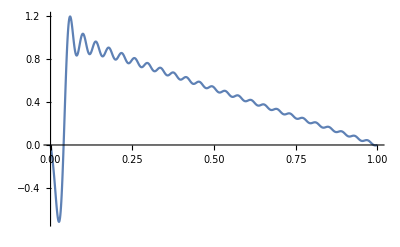

```mathematica
aa1=Transpose[{b,a1}];
q1=ListPlot[aa1,Joined->True]
```

```mathematica
a2=Table[f[1,1,0.3,50,x],{x,0,1,0.001}]
```

{0.,-0.005348,-0.0106416,-0.015828,-0.0208571,-0.0256831,-0.0302656,-0.0345707,-0.038572,-0.0422513,-0.0455989,-0.048614,-0.0513048,-0.0536884,-0.0557898,-0.057642,-0.0592844,-0.0607624,-0.0621257,-0.0634273,-0.0647219,-0.0660644,-0.0675088,-0.0691062,-0.0709039,-0.0729438,-0.0752615,-0.0778851,-0.0808348,-0.0841218,-0.0877485,-0.091708,-0.0959847,-0.100554,-0.105384,-0.110435,-0.115661,-0.121013,-0.126436,-0.131875,-0.137272,-0.142572,-0.147721,-0.15267,-0.157374,-0.161796,-0.165904,-0.169676,-0.173099,-0.176168,-0.178889,-0.181276,-0.183353,-0.185152,-0.186713,-0.188081,-0.18931,-0.190454,-0.191572,-0.192723,-0.193966,-0.195358,-0.196952,-0.198797,-0.200933,-0.203395,-0.206208,-0.20939,-0.212946,-0.216873,-0.221159,-0.225779,-0.230703,-0.23589,-0.241291,-0.246854,-0.25252,-0.258226,-0.26391,-0.269509,-0.274962,-0.280209,-0.285199,-0.289884,-0.294226,-0.298196,-0.301772,-0.304944,-0.307715,-0.310094,-0.312103,-0.313776,-0.315153,-0.316283,-0.317223,-0.318035,-0.318785,-0.319542,-0.320375,-0.32135,-0.322532,-0.323981,-0.32575,-0.327884,-0.330418,-0.333378,-0.336778,-0.340621,-0.3449,-0.349592,-0.354666,-0.360081,-0.365785,-0.371717,-0.377811,-0.383997,-0.390198,-0.396338,-0.402344,-0.408141,-0.413662,-0.418846,-0.423638,-0.427997,-0.431889,-0.435294,-0.438204,-0.440623,-0.44257,-0.444077,-0.445184,-0.445947,-0.446429,-0.446702,-0.446845,-0.446939,-0.447071,-0.447325,-0.447785,-0.44853,-0.449632,-0.451155,-0.453153,-0.455667,-0.458727,-0.462348,-0.466531,-0.47126,-0.476507,-0.482229,-0.48837,-0.494862,-0.501627,-0.508578,-0.515623,-0.522664,-0.529605,-0.536348,-0.5428,-0.548875,-0.554494,-0.559589,-0.564106,-0.568003,-0.571257,-0.573858,-0.575816,-0.577154,-0.577916,-0.57816,-0.577958,-0.577395,-0.576568,-0.575581,-0.574547,-0.573578,-0.572789,-0.572292,-0.572193,-0.572589,-0.573568,-0.575202,-0.577547,-0.580644,-0.584513,-0.589154,-0.594549,-0.600658,-0.607421,-0.614763,-0.622589,-0.630791,-0.639248,-0.647832,-0.656408,-0.664836,-0.67298,-0.680709,-0.687896,-0.69443,-0.700212,-0.705161,-0.709216,-0.712338,-0.71451,-0.715742,-0.716067,-0.715543,-0.71425,-0.712292,-0.709791,-0.706887,-0.703735,-0.700497,-0.697345,-0.69445,-0.691983,-0.690107,-0.688975,-0.688724,-0.689471,-0.691312,-0.694316,-0.698525,-0.703949,-0.710569,-0.718332,-0.727158,-0.736932,-0.747514,-0.75874,-0.770421,-0.782352,-0.794316,-0.806088,-0.817438,-0.828143,-0.837987,-0.846769,-0.854309,-0.860452,-0.865076,-0.86809,-0.869442,-0.869124,-0.867165,-0.863643,-0.858675,-0.852422,-0.845082,-0.836893,-0.828121,-0.819059,-0.810023,-0.80134,-0.793343,-0.786363,-0.780723,-0.776725,-0.774647,-0.774731,-0.777178,-0.782139,-0.789712,-0.799933,-0.812776,-0.828145,-0.845877,-0.865742,-0.887438,-0.910601,-0.934806,-0.959569,-0.98436,-1.00861,-1.0317,-1.05302,-1.07192,-1.08776,-1.09991,-1.10776,-1.11074,-1.10832,-1.10002,-1.08543,-1.06422,-1.03613,-1.00101,-0.958774,-0.909454,-0.853174,-0.790158,-0.720725,-0.645292,-0.564361,-0.478519,-0.388425,-0.294805,-0.198435,-0.100139,-0.000764968,0.0988177,0.197738,0.295135,0.390169,0.482039,0.56999,0.653327,0.731424,0.803735,0.869799,0.929248,0.98181,1.02731,1.06568,1.09695,1.12124,1.13877,1.14984,1.15484,1.15422,1.1485,1.13824,1.12406,1.1066,1.0865,1.06443,1.04104,1.01695,0.992788,0.969102,0.946417,0.925195,0.90584,0.888687,0.874003,0.861982,0.852748,0.846351,0.842774,0.841932,0.843682,0.847825,0.854115,0.862265,0.871957,0.882848,0.894582,0.906796,0.919132,0.931239,0.942788,0.953476,0.963029,0.971214,0.977836,0.982747,0.985846,0.987077,0.986435,0.983959,0.979731,0.973876,0.966553,0.957953,0.948293,0.937809,0.926754,0.915383,0.903955,0.892723,0.881929,0.871795,0.862525,0.854294,0.847246,0.841495,0.837118,0.834157,0.832616,0.832467,0.833644,0.836053,0.839571,0.844047,0.849313,0.855183,0.861461,0.867944,0.87443,0.880717,0.886617,0.891951,0.896562,0.90031,0.903082,0.90479,0.905374,0.904806,0.903084,0.900237,0.89632,0.891415,0.885627,0.879081,0.871918,0.864295,0.856375,0.848326,0.840318,0.832515,0.825076,0.818146,0.811855,0.806318,0.801625,0.797846,0.795026,0.793187,0.792324,0.792408,0.793388,0.79519,0.79772,0.800869,0.804512,0.808515,0.812735,0.817026,0.821245,0.825248,0.828902,0.832084,0.834682,0.836603,0.837771,0.83813,0.837645,0.836303,0.834113,0.831103,0.827324,0.822845,0.817751,0.812141,0.806128,0.799831,0.793378,0.786896,0.780514,0.774356,0.768538,0.763167,0.758338,0.754132,0.75061,0.747819,0.745786,0.744516,0.744,0.744204,0.745081,0.746565,0.748578,0.751025,0.753806,0.75681,0.759923,0.76303,0.766016,0.76877,0.77119,0.773182,0.774662,0.775564,0.775832,0.775431,0.77434,0.772558,0.770099,0.766997,0.763298,0.759066,0.754376,0.749315,0.743978,0.738465,0.732882,0.727334,0.721925,0.716753,0.711912,0.707485,0.703545,0.700149,0.697345,0.695161,0.693612,0.692695,0.692393,0.692672,0.693485,0.69477,0.696455,0.698459,0.700692,0.70306,0.705467,0.707815,0.710009,0.711959,0.713581,0.714801,0.715555,0.715791,0.715471,0.714571,0.713082,0.71101,0.708374,0.70521,0.701565,0.697498,0.693079,0.688387,0.683504,0.67852,0.673526,0.66861,0.663862,0.659363,0.65519,0.651409,0.648077,0.64524,0.64293,0.641166,0.639952,0.63928,0.639127,0.639458,0.640225,0.64137,0.642825,0.644517,0.646364,0.648283,0.650189,0.651998,0.653629,0.655006,0.656058,0.656726,0.656959,0.656718,0.655974,0.654715,0.652938,0.650655,0.647892,0.644683,0.641077,0.637131,0.632911,0.628488,0.623939,0.619344,0.614782,0.610333,0.606073,0.602072,0.598393,0.595091,0.592213,0.589791,0.58785,0.586399,0.585436,0.584947,0.584906,0.585275,0.586008,0.587047,0.588329,0.589784,0.591338,0.592916,0.594442,0.595841,0.597043,0.597981,0.598598,0.598844,0.598678,0.598069,0.597001,0.595465,0.593466,0.591022,0.588159,0.584916,0.581341,0.577489,0.573423,0.569209,0.564921,0.560629,0.556406,0.552322,0.548444,0.544833,0.541542,0.538617,0.536095,0.534001,0.53235,0.531146,0.530382,0.530038,0.530085,0.530485,0.53119,0.532145,0.533289,0.534555,0.535876,0.537181,0.538403,0.539473,0.54033,0.540917,0.541185,0.54109,0.540603,0.539699,0.538368,0.536608,0.53443,0.531855,0.528912,0.525642,0.522091,0.518316,0.514375,0.510333,0.506257,0.502212,0.498266,0.494481,0.490916,0.487624,0.484652,0.482037,0.479807,0.477983,0.476571,0.475571,0.47497,0.474745,0.474866,0.475291,0.475973,0.476858,0.477887,0.478996,0.480123,0.481201,0.482169,0.482966,0.483536,0.483829,0.483804,0.483426,0.482669,0.481518,0.479967,0.47802,0.475692,0.473006,0.469996,0.466703,0.463174,0.459463,0.455628,0.451731,0.447834,0.443999,0.440287,0.436755,0.433455,0.430435,0.427733,0.425381,0.4234,0.421805,0.420597,0.41977,0.419309,0.419186,0.419369,0.419816,0.420478,0.421303,0.422233,0.423208,0.424167,0.425051,0.425801,0.426362,0.426685,0.426726,0.426449,0.425826,0.424837,0.423472,0.421731,0.419622,0.417164,0.414383,0.411315,0.408002,0.404491,0.400836,0.397094,0.393323,0.389582,0.385929,0.382421,0.37911,0.376042,0.373258,0.370793,0.36867,0.366908,0.365513,0.364483,0.363809,0.363469,0.363436,0.363673,0.364139,0.364784,0.365556,0.366398,0.367255,0.368067,0.368779,0.369337,0.36969,0.369794,0.369612,0.369112,0.368272,0.367078,0.365524,0.363614,0.361362,0.358788,0.355923,0.352803,0.349472,0.345978,0.342373,0.338713,0.335054,0.331453,0.327963,0.324637,0.321523,0.318662,0.316091,0.313836,0.311919,0.310352,0.309136,0.308267,0.307729,0.307499,0.307546,0.307832,0.308314,0.308944,0.309668,0.310432,0.311182,0.311862,0.312418,0.312802,0.312968,0.312875,0.312491,0.31179,0.310753,0.309373,0.307647,0.305585,0.303202,0.300524,0.297583,0.294416,0.291069,0.28759,0.284031,0.280446,0.276889,0.273415,0.270073,0.266914,0.263979,0.261308,0.258929,0.256868,0.255139,0.25375,0.252699,0.251976,0.251562,0.251432,0.251553,0.251884,0.252382,0.252996,0.253677,0.254369,0.255021,0.255578,0.255992,0.256216,0.256209,0.255934,0.255364,0.254477,0.253259,0.251707,0.249823,0.24762,0.245117,0.242343,0.23933,0.236121,0.232759,0.229294,0.225777,0.222261,0.2188,0.215443,0.21224,0.209235,0.206467,0.203971,0.201773,0.199891,0.198338,0.197114,0.196216,0.19563,0.195332,0.195296,0.195485,0.195858,0.19637,0.196971,0.19761,0.198235,0.198795,0.199238,0.199518,0.199592,0.199422,0.198977,0.198232,0.197171,0.195784,0.19407,0.192038,0.189702,0.187086,0.184221,0.181142,0.177891,0.174516,0.171064,0.167587,0.164137,0.160765,0.15752,0.154447,0.151588,0.148979,0.146649,0.14462,0.142909,0.141521,0.140455,0.139702,0.139244,0.139057,0.13911,0.139364,0.139776,0.140302,0.14089,0.14149,0.142051,0.142522,0.142857,0.143009,0.142941,0.142616,0.142009,0.141097,0.139869,0.13832,0.136453,0.134278,0.131816,0.129092,0.12614,0.122997,0.119708,0.116319,0.11288,0.109442,0.106055,0.102769,0.0996307,0.0966829,0.093964,0.0915064,0.089336,0.0874713,0.0859232,0.0846944,0.0837799,0.0831663,0.0828331,0.0827524,0.08289,0.0832064,0.0836574,0.0841955,0.084771,0.0853333,0.0858322,0.086219,0.086448,0.0864775,0.0862706,0.0857967,0.0850318,0.0839593,0.0825702,0.0808637,0.078847,0.076535,0.0739501,0.0711217,0.068085,0.0648808,0.061554,0.0581524,0.054726,0.0513252,0.0479997,0.0447974,0.041763,0.0389371,0.0363547,0.0340451,0.0320303,0.0303251,0.0289364,0.0278631,0.0270962,0.0266189,0.0264071,0.0264301,0.0266512,0.0270286,0.0275169,0.0280675,0.0286306,0.0291558,0.0295938,0.0298975,0.0300233,0.0299318,0.0295894,0.0289687,0.0280493,0.0268184,0.025271,0.0234101,0.0212468,0.0187994,0.0160939,0.0131623,0.0100428,0.00677788,0.003414,4.41085×10^-16}

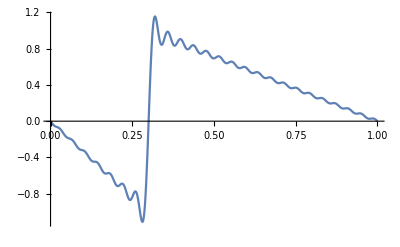

```mathematica
aa2=Transpose[{b,a2}];
q2=ListPlot[aa2,Joined->True]
```

```mathematica
a3=Table[f[1,1,0.6,50,x],{x,0,1,0.001}]
```

{0.,0.000321031,0.000591622,0.000762614,0.00078737,0.000622964,0.000231263,-0.000420101,-0.00135691,-0.00259772,-0.00415335,-0.00602667,-0.00821247,-0.0106976,-0.0134614,-0.0164759,-0.0197072,-0.0231154,-0.0266564,-0.0302827,-0.0339446,-0.0375915,-0.041173,-0.0446405,-0.0479485,-0.051055,-0.0539236,-0.0565236,-0.0588313,-0.0608304,-0.0625122,-0.0638764,-0.0649304,-0.0656897,-0.0661772,-0.0664227,-0.0664623,-0.0663371,-0.0660925,-0.065777,-0.0654409,-0.065135,-0.0649094,-0.0648121,-0.0648881,-0.0651776,-0.0657159,-0.0665317,-0.0676467,-0.0690752,-0.0708232,-0.0728891,-0.0752627,-0.0779264,-0.080855,-0.0840166,-0.0873735,-0.0908828,-0.0944979,-0.0981694,-0.101846,-0.105478,-0.109014,-0.112407,-0.115614,-0.118594,-0.121315,-0.123749,-0.125876,-0.127686,-0.129173,-0.130343,-0.131207,-0.131786,-0.132107,-0.132204,-0.132116,-0.131889,-0.131569,-0.131208,-0.130856,-0.130566,-0.130386,-0.130365,-0.130543,-0.130961,-0.13165,-0.132634,-0.133931,-0.135552,-0.137498,-0.139761,-0.142328,-0.145175,-0.148273,-0.151586,-0.155072,-0.158685,-0.162376,-0.166095,-0.169787,-0.173403,-0.176892,-0.180209,-0.18331,-0.18616,-0.188727,-0.190989,-0.192931,-0.194544,-0.19583,-0.196798,-0.197465,-0.197856,-0.198004,-0.197946,-0.197727,-0.197393,-0.196995,-0.196586,-0.196219,-0.195945,-0.195813,-0.19587,-0.196156,-0.196708,-0.197553,-0.198714,-0.200203,-0.202025,-0.204177,-0.206648,-0.209417,-0.212456,-0.215732,-0.219204,-0.222826,-0.226549,-0.23032,-0.234087,-0.237796,-0.241395,-0.244835,-0.24807,-0.251061,-0.253772,-0.256178,-0.258259,-0.260003,-0.261408,-0.26248,-0.263234,-0.263692,-0.263885,-0.263849,-0.263627,-0.263267,-0.26282,-0.262339,-0.26188,-0.261495,-0.261239,-0.261158,-0.261299,-0.261701,-0.262396,-0.263409,-0.264758,-0.266451,-0.26849,-0.270864,-0.273556,-0.276542,-0.279789,-0.283256,-0.286898,-0.290666,-0.294507,-0.298365,-0.302184,-0.305911,-0.309492,-0.312878,-0.316026,-0.318896,-0.321458,-0.323689,-0.325572,-0.327103,-0.328283,-0.329123,-0.329645,-0.329876,-0.329853,-0.329617,-0.329216,-0.328703,-0.328133,-0.327562,-0.327047,-0.326645,-0.326407,-0.326383,-0.326616,-0.327143,-0.327995,-0.329192,-0.330748,-0.332666,-0.334941,-0.337559,-0.340496,-0.34372,-0.347194,-0.350871,-0.354702,-0.358631,-0.362601,-0.366555,-0.370432,-0.374178,-0.377739,-0.381066,-0.384117,-0.386854,-0.389251,-0.391287,-0.392952,-0.394244,-0.395173,-0.395756,-0.396019,-0.395998,-0.395733,-0.395274,-0.394674,-0.39399,-0.393282,-0.39261,-0.392034,-0.39161,-0.391394,-0.391433,-0.391769,-0.392438,-0.393466,-0.394871,-0.396659,-0.398831,-0.401373,-0.404266,-0.407479,-0.410973,-0.414704,-0.41862,-0.422663,-0.426775,-0.430893,-0.434954,-0.438898,-0.442666,-0.446204,-0.449464,-0.452403,-0.454989,-0.457196,-0.459009,-0.460424,-0.461445,-0.462087,-0.462374,-0.462341,-0.462029,-0.461487,-0.460772,-0.459942,-0.459062,-0.458195,-0.457406,-0.456759,-0.456312,-0.45612,-0.456232,-0.456688,-0.457521,-0.458754,-0.460399,-0.462459,-0.464925,-0.467778,-0.470991,-0.474526,-0.478335,-0.482367,-0.486561,-0.490854,-0.495179,-0.49947,-0.503658,-0.507679,-0.511473,-0.514984,-0.518164,-0.520972,-0.523379,-0.525363,-0.526914,-0.528032,-0.528731,-0.529033,-0.528969,-0.528584,-0.527927,-0.527056,-0.526035,-0.524932,-0.523817,-0.522761,-0.521833,-0.5211,-0.520625,-0.520463,-0.520662,-0.521263,-0.522293,-0.523773,-0.525708,-0.528094,-0.530915,-0.534145,-0.537746,-0.54167,-0.545861,-0.550257,-0.55479,-0.559386,-0.563972,-0.568472,-0.572815,-0.576931,-0.580756,-0.584234,-0.587316,-0.589964,-0.592151,-0.59386,-0.595087,-0.595841,-0.596143,-0.596023,-0.595527,-0.594705,-0.59362,-0.592341,-0.590941,-0.589498,-0.588091,-0.586798,-0.585697,-0.584858,-0.584347,-0.584222,-0.584532,-0.585314,-0.586593,-0.588382,-0.590683,-0.593481,-0.596753,-0.600459,-0.604551,-0.608969,-0.613646,-0.618506,-0.623469,-0.628452,-0.63337,-0.63814,-0.64268,-0.646918,-0.650783,-0.654218,-0.657174,-0.659615,-0.661517,-0.66287,-0.663678,-0.663959,-0.663744,-0.663078,-0.662016,-0.660625,-0.658981,-0.657167,-0.65527,-0.65338,-0.651589,-0.649985,-0.648654,-0.647675,-0.647117,-0.647042,-0.647499,-0.648521,-0.650131,-0.652335,-0.655125,-0.658476,-0.662351,-0.666697,-0.67145,-0.676536,-0.681868,-0.687356,-0.692904,-0.698412,-0.703782,-0.708918,-0.71373,-0.718133,-0.722053,-0.725429,-0.728212,-0.730367,-0.731876,-0.732736,-0.732962,-0.732585,-0.731651,-0.73022,-0.728368,-0.72618,-0.72375,-0.721183,-0.718584,-0.716063,-0.713728,-0.711682,-0.710025,-0.708846,-0.708222,-0.708219,-0.708885,-0.710255,-0.712343,-0.715147,-0.718645,-0.7228,-0.727553,-0.732834,-0.738556,-0.74462,-0.750917,-0.757332,-0.763744,-0.770031,-0.776073,-0.781756,-0.786971,-0.791622,-0.795626,-0.798913,-0.801433,-0.803154,-0.804065,-0.804174,-0.80351,-0.802123,-0.800082,-0.797472,-0.794396,-0.790968,-0.787316,-0.783571,-0.779873,-0.776359,-0.773164,-0.77042,-0.768245,-0.766746,-0.766016,-0.766128,-0.767134,-0.769065,-0.77193,-0.775711,-0.78037,-0.785843,-0.792046,-0.798874,-0.806205,-0.813902,-0.821815,-0.829788,-0.83766,-0.845268,-0.852456,-0.859074,-0.864983,-0.870063,-0.874209,-0.877341,-0.879401,-0.880359,-0.880212,-0.878985,-0.876732,-0.873532,-0.869493,-0.864744,-0.859435,-0.853736,-0.847828,-0.841901,-0.836152,-0.830775,-0.82596,-0.821889,-0.818724,-0.816614,-0.815679,-0.816014,-0.817686,-0.820726,-0.825133,-0.83087,-0.837866,-0.846016,-0.855182,-0.865197,-0.875869,-0.886982,-0.898303,-0.909589,-0.92059,-0.931055,-0.940741,-0.949416,-0.956867,-0.962906,-0.967375,-0.970151,-0.971148,-0.970326,-0.967685,-0.963276,-0.957193,-0.949578,-0.940616,-0.930532,-0.919589,-0.908083,-0.896334,-0.884682,-0.873479,-0.863078,-0.853831,-0.846073,-0.84012,-0.836256,-0.834725,-0.835726,-0.839406,-0.845852,-0.855085,-0.867061,-0.881665,-0.89871,-0.917938,-0.939024,-0.961573,-0.985133,-1.00919,-1.0332,-1.05656,-1.07863,-1.09879,-1.11637,-1.13072,-1.14121,-1.14723,-1.14821,-1.14364,-1.13304,-1.11602,-1.09229,-1.0616,-1.02383,-0.978936,-0.926973,-0.868104,-0.802586,-0.730776,-0.653121,-0.570155,-0.482494,-0.390822,-0.295885,-0.19848,-0.0994389,0.00037962,0.100106,0.198871,0.295821,0.390132,0.481017,0.567745,0.649646,0.726123,0.79666,0.860831,0.9183,0.968831,1.01228,1.04862,1.07791,1.10028,1.116,1.12538,1.12883,1.12682,1.11987,1.10855,1.09347,1.07527,1.05459,1.03208,1.00836,0.984061,0.959752,0.935978,0.913233,0.891953,0.872514,0.855227,0.840334,0.828006,0.818348,0.811393,0.807111,0.805408,0.806135,0.809093,0.814038,0.820691,0.828743,0.837868,0.847726,0.857976,0.86828,0.878314,0.887774,0.896381,0.903889,0.910086,0.914804,0.917913,0.919331,0.919019,0.916981,0.913266,0.90796,0.901186,0.893102,0.883889,0.873754,0.862918,0.851614,0.840078,0.828547,0.817249,0.8064,0.796198,0.786822,0.778421,0.771119,0.765008,0.760149,0.756567,0.754257,0.753182,0.753274,0.754438,0.756554,0.759483,0.763067,0.767135,0.771509,0.776007,0.780448,0.784658,0.788471,0.791734,0.794314,0.796097,0.796989,0.796925,0.795862,0.793784,0.790702,0.78665,0.781689,0.775899,0.76938,0.762249,0.754636,0.746681,0.738529,0.730328,0.722224,0.714359,0.706864,0.699861,0.693456,0.687738,0.682776,0.67862,0.675299,0.672819,0.671165,0.670301,0.670174,0.670709,0.671818,0.673401,0.675343,0.677528,0.67983,0.682125,0.684291,0.686211,0.687775,0.688884,0.689454,0.689413,0.688709,0.687305,0.685182,0.682343,0.678805,0.674606,0.669799,0.66445,0.658641,0.652463,0.646015,0.639401,0.63273,0.626109,0.619643,0.613431,0.607566,0.602129,0.597189,0.592804,0.589013,0.585844,0.583304,0.581387,0.580071,0.579318,0.579076,0.579281,0.579858,0.580723,0.581788,0.582958,0.584137,0.585232,0.58615,0.586807,0.587123,0.587031,0.586474,0.585406,0.583796,0.581628,0.578899,0.575622,0.571821,0.567536,0.562818,0.557728,0.552338,0.546724,0.540968,0.535157,0.529375,0.523707,0.518233,0.513028,0.508158,0.503682,0.499645,0.496084,0.493022,0.490467,0.488417,0.486854,0.485752,0.485068,0.484753,0.484747,0.484983,0.485389,0.485887,0.4864,0.48685,0.487161,0.487264,0.487091,0.486586,0.4857,0.484395,0.482643,0.48043,0.47775,0.474614,0.471041,0.467062,0.462718,0.458061,0.453148,0.448044,0.442817,0.437538,0.43228,0.427114,0.422108,0.417324,0.412821,0.408649,0.404846,0.401446,0.398467,0.39592,0.393801,0.3921,0.39079,0.38984,0.389207,0.38884,0.388683,0.388672,0.388744,0.388831,0.388866,0.388783,0.388523,0.388026,0.387244,0.386134,0.384662,0.382803,0.380544,0.377881,0.37482,0.371379,0.367584,0.363471,0.359084,0.354472,0.349693,0.344805,0.339871,0.334955,0.330119,0.325423,0.320923,0.316669,0.312706,0.30907,0.305788,0.302879,0.300352,0.298205,0.296426,0.294996,0.293885,0.293054,0.292461,0.292053,0.291776,0.291572,0.29138,0.291141,0.290797,0.290292,0.289575,0.288601,0.287332,0.285737,0.283794,0.28149,0.278822,0.275797,0.272428,0.26874,0.264765,0.260543,0.25612,0.251545,0.246874,0.242163,0.23747,0.232852,0.228363,0.224054,0.219971,0.216156,0.21264,0.209449,0.2066,0.204101,0.20195,0.200137,0.198643,0.19744,0.196495,0.195766,0.195206,0.194764,0.194386,0.194017,0.193602,0.193087,0.192421,0.191555,0.190449,0.189067,0.187381,0.185371,0.183024,0.180337,0.177317,0.173979,0.170343,0.166442,0.162311,0.157994,0.153539,0.148997,0.14442,0.139864,0.135381,0.131024,0.126838,0.12287,0.119155,0.115725,0.112604,0.109807,0.107341,0.105205,0.103388,0.101872,0.100631,0.0996326,0.0988359,0.0981968,0.0976667,0.0971941,0.0967262,0.0962102,0.0955944,0.0948301,0.0938722,0.092681,0.0912227,0.0894706,0.0874056,0.0850167,0.0823015,0.0792659,0.0759243,0.0722988,0.0684191,0.0643213,0.0600473,0.0556432,0.0511589,0.0466461,0.042157,0.0377436,0.0334555,0.0293392,0.0254367,0.0217844,0.018412,0.0153423,0.0125898,0.0101611,0.00805402,0.00625838,0.0047557,0.00351992,0.00251807,0.00171109,0.00105489,0.000501422,-8.10564×10^-16}

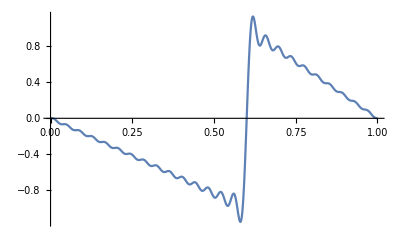

```mathematica
aa3=Transpose[{b,a3}];
q3=ListPlot[aa3,Joined->True]
```

```mathematica
a4=Table[f[1,1,0.61,50,x],{x,0,1,0.001}]
```

{0.,-0.000233718,-0.000502041,-0.000838724,-0.00127584,-0.00184299,-0.00256659,-0.00346919,-0.00456895,-0.00587917,-0.00740798,-0.00915814,-0.011127,-0.0133063,-0.015683,-0.018239,-0.0209515,-0.0237944,-0.026738,-0.0297501,-0.0327971,-0.0358442,-0.0388568,-0.0418011,-0.0446449,-0.0473585,-0.0499155,-0.0522931,-0.0544732,-0.0564423,-0.0581922,-0.0597201,-0.0610287,-0.0621259,-0.0630251,-0.0637444,-0.0643063,-0.0647373,-0.065067,-0.0653277,-0.0655533,-0.0657786,-0.0660383,-0.0663666,-0.0667956,-0.0673554,-0.0680725,-0.0689698,-0.0700657,-0.0713737,-0.0729021,-0.0746538,-0.0766263,-0.0788114,-0.0811959,-0.0837616,-0.0864858,-0.089342,-0.0923002,-0.0953282,-0.0983917,-0.101456,-0.104485,-0.107446,-0.110305,-0.113032,-0.115601,-0.117988,-0.120176,-0.122149,-0.1239,-0.125426,-0.126729,-0.127817,-0.128704,-0.129408,-0.129951,-0.130362,-0.130669,-0.130905,-0.131106,-0.131305,-0.13154,-0.131844,-0.13225,-0.132789,-0.133489,-0.134372,-0.135457,-0.136759,-0.138286,-0.14004,-0.142021,-0.144218,-0.146619,-0.149206,-0.151956,-0.15484,-0.157829,-0.16089,-0.163988,-0.167086,-0.17015,-0.173143,-0.176033,-0.178787,-0.18138,-0.183786,-0.185988,-0.187969,-0.189723,-0.191245,-0.192538,-0.19361,-0.194475,-0.195152,-0.195663,-0.196037,-0.196305,-0.196499,-0.196656,-0.196811,-0.197003,-0.197265,-0.197633,-0.198137,-0.198807,-0.199666,-0.200733,-0.202024,-0.203548,-0.205307,-0.207299,-0.209517,-0.211945,-0.214566,-0.217355,-0.220284,-0.223322,-0.226435,-0.229587,-0.23274,-0.235856,-0.238901,-0.241838,-0.244635,-0.247264,-0.2497,-0.251923,-0.253918,-0.255676,-0.257192,-0.258471,-0.259519,-0.260351,-0.260987,-0.261451,-0.26177,-0.261979,-0.26211,-0.262202,-0.262293,-0.26242,-0.262621,-0.262931,-0.263385,-0.26401,-0.264834,-0.265875,-0.267151,-0.268669,-0.270435,-0.272444,-0.27469,-0.277157,-0.279827,-0.282673,-0.285666,-0.288775,-0.291962,-0.29519,-0.298421,-0.301613,-0.30473,-0.307735,-0.310593,-0.313274,-0.315752,-0.318006,-0.320019,-0.321782,-0.323292,-0.32455,-0.325565,-0.326352,-0.32693,-0.327327,-0.327571,-0.327697,-0.327741,-0.327743,-0.327743,-0.327781,-0.327897,-0.328128,-0.328511,-0.329075,-0.329849,-0.330855,-0.332108,-0.33362,-0.335394,-0.337427,-0.339712,-0.342232,-0.344968,-0.347892,-0.350974,-0.354179,-0.357468,-0.360801,-0.364137,-0.367433,-0.37065,-0.373746,-0.376687,-0.379439,-0.381975,-0.38427,-0.386309,-0.388081,-0.389581,-0.390811,-0.391781,-0.392506,-0.393008,-0.393313,-0.393455,-0.393469,-0.393395,-0.393275,-0.393152,-0.39307,-0.39307,-0.393195,-0.393481,-0.393963,-0.394671,-0.395627,-0.396851,-0.398353,-0.400138,-0.402204,-0.40454,-0.407132,-0.409957,-0.412987,-0.416187,-0.419522,-0.422948,-0.426423,-0.429901,-0.433337,-0.436687,-0.439908,-0.44296,-0.445807,-0.44842,-0.450773,-0.452846,-0.454629,-0.456116,-0.457309,-0.458219,-0.458861,-0.459259,-0.459443,-0.459447,-0.459311,-0.459078,-0.458794,-0.458505,-0.458261,-0.458106,-0.458087,-0.458244,-0.458615,-0.459233,-0.460124,-0.461307,-0.462796,-0.464596,-0.466705,-0.469112,-0.4718,-0.474745,-0.477916,-0.481276,-0.484785,-0.488396,-0.492061,-0.495731,-0.499356,-0.502886,-0.506274,-0.509476,-0.512453,-0.515171,-0.5176,-0.519721,-0.521518,-0.522988,-0.524131,-0.524959,-0.525489,-0.525747,-0.525766,-0.525584,-0.525245,-0.524797,-0.52429,-0.523779,-0.523314,-0.522949,-0.522734,-0.522716,-0.522936,-0.523432,-0.524233,-0.525362,-0.526833,-0.528653,-0.53082,-0.533322,-0.536142,-0.53925,-0.542614,-0.546193,-0.549939,-0.553802,-0.557728,-0.56166,-0.565542,-0.569319,-0.572937,-0.576345,-0.579499,-0.58236,-0.584895,-0.58708,-0.588899,-0.590344,-0.591419,-0.592135,-0.592511,-0.592576,-0.592368,-0.591929,-0.591309,-0.590564,-0.58975,-0.588929,-0.58816,-0.587504,-0.587018,-0.586756,-0.586767,-0.587093,-0.587769,-0.588821,-0.590267,-0.592115,-0.594363,-0.596999,-0.600001,-0.603339,-0.606973,-0.610856,-0.614936,-0.619152,-0.623444,-0.627745,-0.63199,-0.636114,-0.640054,-0.643754,-0.647158,-0.650221,-0.652905,-0.655182,-0.65703,-0.658443,-0.659421,-0.659977,-0.660133,-0.659924,-0.659392,-0.658587,-0.657567,-0.656396,-0.655143,-0.653878,-0.652672,-0.651597,-0.650721,-0.650109,-0.649818,-0.649898,-0.650394,-0.651335,-0.652745,-0.654634,-0.656999,-0.659828,-0.663096,-0.666768,-0.670795,-0.675125,-0.679691,-0.684426,-0.689254,-0.694096,-0.698875,-0.703511,-0.707928,-0.712057,-0.715831,-0.719195,-0.722102,-0.724514,-0.726407,-0.72777,-0.728603,-0.728921,-0.728749,-0.728129,-0.72711,-0.725753,-0.72413,-0.722318,-0.720399,-0.718461,-0.716593,-0.714882,-0.713412,-0.712264,-0.711511,-0.711216,-0.711434,-0.712206,-0.713559,-0.71551,-0.718057,-0.721186,-0.724866,-0.729056,-0.733697,-0.738722,-0.744052,-0.749599,-0.755269,-0.760965,-0.766585,-0.772031,-0.777205,-0.782016,-0.78638,-0.790224,-0.793485,-0.796115,-0.798081,-0.799364,-0.799964,-0.799895,-0.799192,-0.797901,-0.796088,-0.79383,-0.791216,-0.788347,-0.785331,-0.782281,-0.779313,-0.776542,-0.774081,-0.772037,-0.770508,-0.769581,-0.76933,-0.769813,-0.771071,-0.773128,-0.775985,-0.779627,-0.784019,-0.789103,-0.794808,-0.801044,-0.807706,-0.814676,-0.821829,-0.829029,-0.836142,-0.843027,-0.849551,-0.855586,-0.861012,-0.865723,-0.869629,-0.872657,-0.874754,-0.875891,-0.87606,-0.875276,-0.873581,-0.871038,-0.867732,-0.86377,-0.859277,-0.854394,-0.849274,-0.844081,-0.838982,-0.834149,-0.829747,-0.82594,-0.822875,-0.82069,-0.8195,-0.819402,-0.820467,-0.822738,-0.826232,-0.830935,-0.836801,-0.843758,-0.851703,-0.860505,-0.87001,-0.880041,-0.890404,-0.900891,-0.911284,-0.921362,-0.930903,-0.939694,-0.947532,-0.954231,-0.959627,-0.963582,-0.965991,-0.96678,-0.965915,-0.9634,-0.959279,-0.953637,-0.946601,-0.938335,-0.92904,-0.91895,-0.908328,-0.89746,-0.88665,-0.876214,-0.866472,-0.857743,-0.850333,-0.844534,-0.840608,-0.83879,-0.839272,-0.842201,-0.847675,-0.855734,-0.86636,-0.879471,-0.894923,-0.912508,-0.931952,-0.952923,-0.97503,-0.99783,-1.02083,-1.0435,-1.06528,-1.08558,-1.10379,-1.11932,-1.13156,-1.13993,-1.14388,-1.14288,-1.13646,-1.12422,-1.10579,-1.08091,-1.04937,-1.01106,-0.965959,-0.914125,-0.855716,-0.790978,-0.720249,-0.643948,-0.562577,-0.47671,-0.386987,-0.294106,-0.198812,-0.101884,-0.00412848,0.0936365,0.190591,0.285927,0.37886,0.468637,0.554554,0.635962,0.712274,0.78298,0.847646,0.905926,0.957561,1.00238,1.04032,1.07139,1.09569,1.11343,1.12487,1.13037,1.13033,1.12524,1.11562,1.10203,1.08507,1.06534,1.04347,1.02008,0.995752,0.971085,0.946622,0.92287,0.90029,0.879289,0.860214,0.84335,0.828918,0.817071,0.807898,0.80142,0.797599,0.796337,0.797483,0.800838,0.806161,0.813176,0.821581,0.831054,0.841261,0.851866,0.862534,0.872945,0.882796,0.891806,0.899727,0.906343,0.911479,0.914997,0.916806,0.916854,0.915136,0.911686,0.906581,0.89993,0.891881,0.882608,0.872307,0.861197,0.849507,0.837475,0.825339,0.813336,0.801689,0.790611,0.780293,0.770906,0.762591,0.755462,0.749601,0.745058,0.74185,0.739962,0.739347,0.73993,0.741607,0.74425,0.747712,0.751829,0.756425,0.761315,0.766311,0.771228,0.775885,0.78011,0.783748,0.786658,0.788722,0.789841,0.789945,0.788987,0.786947,0.783832,0.779674,0.774532,0.768484,0.761632,0.754093,0.746002,0.737501,0.728743,0.719883,0.711076,0.702474,0.69422,0.686448,0.679279,0.672814,0.667139,0.662317,0.658391,0.655382,0.653286,0.652079,0.651715,0.652128,0.653235,0.654937,0.65712,0.659663,0.662436,0.665305,0.668136,0.670798,0.673166,0.675122,0.676561,0.677392,0.67754,0.676947,0.675573,0.673399,0.670426,0.666672,0.662176,0.656994,0.651198,0.644874,0.638121,0.631045,0.62376,0.616385,0.609038,0.601835,0.594889,0.588305,0.582176,0.576585,0.571601,0.567276,0.563647,0.560733,0.558536,0.557038,0.556207,0.555994,0.556335,0.557154,0.558364,0.559868,0.561564,0.563345,0.565106,0.566738,0.568143,0.569223,0.569893,0.570077,0.569712,0.56875,0.567155,0.56491,0.562013,0.558477,0.554331,0.549619,0.544399,0.538739,0.53272,0.526429,0.519958,0.513406,0.506871,0.50045,0.494236,0.488318,0.482775,0.477678,0.473085,0.469043,0.465583,0.462723,0.460467,0.458802,0.457701,0.457126,0.457024,0.45733,0.457972,0.45887,0.459935,0.461079,0.462209,0.463236,0.464071,0.464633,0.464847,0.464647,0.463977,0.462794,0.461068,0.458781,0.45593,0.452525,0.44859,0.444162,0.43929,0.434033,0.42846,0.422645,0.41667,0.41062,0.404581,0.398637,0.392872,0.387363,0.38218,0.377386,0.373034,0.369165,0.36581,0.362983,0.36069,0.358921,0.357653,0.356853,0.356474,0.356461,0.35675,0.357269,0.357941,0.358686,0.359422,0.360069,0.360548,0.360786,0.360714,0.360272,0.359411,0.35809,0.356281,0.353968,0.351146,0.347824,0.344022,0.339774,0.335122,0.33012,0.324828,0.319314,0.313653,0.307921,0.302195,0.296553,0.291071,0.28582,0.280865,0.276263,0.272063,0.268304,0.265014,0.262208,0.259892,0.258056,0.256682,0.255739,0.255186,0.254971,0.255036,0.255315,0.255739,0.256232,0.256721,0.257128,0.257383,0.257416,0.257164,0.256572,0.25559,0.254183,0.252323,0.249993,0.24719,0.24392,0.240202,0.236066,0.231552,0.226708,0.221592,0.216266,0.210799,0.205263,0.199731,0.194276,0.188969,0.183877,0.179062,0.174577,0.17047,0.166778,0.163528,0.160734,0.158403,0.156527,0.155089,0.154059,0.1534,0.153063,0.152994,0.15313,0.153405,0.153749,0.15409,0.154356,0.154479,0.154392,0.154035,0.153354,0.152303,0.150846,0.148957,0.146618,0.143826,0.140586,0.136917,0.132845,0.128408,0.123654,0.118635,0.113414,0.108055,0.102627,0.0972013,0.0918479,0.0866353,0.0816283,0.076887,0.0724646,0.0684064,0.0647487,0.0615182,0.0587308,0.0563916,0.0544946,0.053023,0.0519498,0.0512377,0.0508411,0.0507064,0.0507736,0.0509779,0.0512511,0.0515234,0.0517249,0.0517878,0.0516474,0.0512442,0.0505253,0.0494452,0.0479678,0.0460663,0.0437247,0.0409376,0.0377106,0.0340602,0.0300131,0.0256059,0.0208841,0.0159007,0.0107153,0.00539245,2.12113×10^-16}

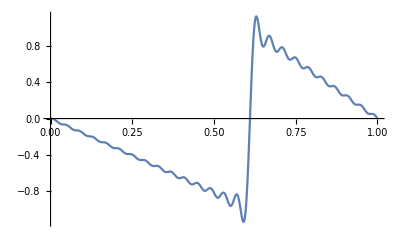

```mathematica
aa4=Transpose[{b,a4}];
q4=ListPlot[aa4,Joined->True]
```

```mathematica
a5=Table[f[1,1,0.96,50,x],{x,0,1,0.001}]
```

{0.,0.000940399,0.00183101,0.0026233,0.00327119,0.00373224,0.00396871,0.00394848,0.00364588,0.00304233,0.00212683,0.000896177,-0.000644886,-0.00248384,-0.00460066,-0.00696838,-0.00955369,-0.0123178,-0.0152176,-0.0182062,-0.0212349,-0.0242537,-0.0272129,-0.0300644,-0.0327626,-0.0352661,-0.0375379,-0.0395472,-0.0412697,-0.0426882,-0.0437931,-0.0445829,-0.0450638,-0.0452499,-0.0451627,-0.0448303,-0.0442874,-0.0435736,-0.042733,-0.041813,-0.0408627,-0.0399323,-0.0390712,-0.0383272,-0.0377453,-0.0373663,-0.0372259,-0.0373538,-0.0377731,-0.0384995,-0.039541,-0.0408976,-0.0425615,-0.0445172,-0.0467418,-0.0492056,-0.051873,-0.0547032,-0.0576513,-0.0606694,-0.0637079,-0.0667167,-0.0696462,-0.0724492,-0.0750812,-0.0775023,-0.0796777,-0.081579,-0.0831843,-0.0844794,-0.0854579,-0.0861212,-0.0864788,-0.0865476,-0.0863522,-0.0859233,-0.0852979,-0.0845178,-0.0836288,-0.0826792,-0.081719,-0.0807987,-0.0799674,-0.0792723,-0.078757,-0.0784608,-0.0784174,-0.078654,-0.0791912,-0.0800416,-0.0812103,-0.0826942,-0.0844822,-0.0865559,-0.0888893,-0.0914503,-0.0942006,-0.0970975,-0.100094,-0.103142,-0.106191,-0.109189,-0.112089,-0.114842,-0.117407,-0.119745,-0.121823,-0.123614,-0.125101,-0.126271,-0.127121,-0.127656,-0.127889,-0.127839,-0.127533,-0.127006,-0.126297,-0.12545,-0.124512,-0.123532,-0.122562,-0.121652,-0.120851,-0.120206,-0.119758,-0.119547,-0.119602,-0.119949,-0.120606,-0.121583,-0.122881,-0.124495,-0.126409,-0.128603,-0.131047,-0.133707,-0.136542,-0.139507,-0.142553,-0.145632,-0.14869,-0.151678,-0.154547,-0.15725,-0.159746,-0.161999,-0.163977,-0.165656,-0.167021,-0.168063,-0.168783,-0.169186,-0.169291,-0.169119,-0.168702,-0.168075,-0.16728,-0.166364,-0.165375,-0.164365,-0.163385,-0.162486,-0.161716,-0.161122,-0.160744,-0.160619,-0.160775,-0.161236,-0.162016,-0.163123,-0.164554,-0.166301,-0.168345,-0.170662,-0.17322,-0.175982,-0.178903,-0.181938,-0.185036,-0.188145,-0.191213,-0.194191,-0.197028,-0.199679,-0.202105,-0.204269,-0.206144,-0.207708,-0.208948,-0.209858,-0.210442,-0.210711,-0.210683,-0.210386,-0.209853,-0.209123,-0.20824,-0.207253,-0.206212,-0.205171,-0.20418,-0.203292,-0.202555,-0.202013,-0.201707,-0.201671,-0.201933,-0.202512,-0.203419,-0.20466,-0.206229,-0.208113,-0.210292,-0.212737,-0.215413,-0.21828,-0.221291,-0.224398,-0.227549,-0.23069,-0.233769,-0.236735,-0.239539,-0.242136,-0.244488,-0.246561,-0.248329,-0.249773,-0.250883,-0.251656,-0.2521,-0.252228,-0.252063,-0.251635,-0.250981,-0.250144,-0.249169,-0.248108,-0.247014,-0.245939,-0.244938,-0.244062,-0.243358,-0.242872,-0.242641,-0.242699,-0.24307,-0.243771,-0.244812,-0.246193,-0.247906,-0.249934,-0.252253,-0.254832,-0.257631,-0.260608,-0.263713,-0.266896,-0.270102,-0.273276,-0.276366,-0.27932,-0.282089,-0.28463,-0.286905,-0.288882,-0.290538,-0.291856,-0.292829,-0.293459,-0.293755,-0.293735,-0.293426,-0.292862,-0.292081,-0.291131,-0.29006,-0.288922,-0.28777,-0.286662,-0.285649,-0.284785,-0.284117,-0.283689,-0.283538,-0.283694,-0.284181,-0.285011,-0.286193,-0.287721,-0.289586,-0.291765,-0.294233,-0.296952,-0.299882,-0.302974,-0.306179,-0.309441,-0.312705,-0.315915,-0.319017,-0.321958,-0.32469,-0.327171,-0.329364,-0.331239,-0.332776,-0.333961,-0.33479,-0.335267,-0.335407,-0.335231,-0.334769,-0.33406,-0.333145,-0.332075,-0.330902,-0.329682,-0.32847,-0.327325,-0.326301,-0.32545,-0.324821,-0.324454,-0.324388,-0.324649,-0.325258,-0.326226,-0.327557,-0.329243,-0.331269,-0.33361,-0.336235,-0.339104,-0.342172,-0.345389,-0.348699,-0.352046,-0.355372,-0.358619,-0.361733,-0.36466,-0.367353,-0.36977,-0.371875,-0.373642,-0.375052,-0.376094,-0.376768,-0.377083,-0.377055,-0.376712,-0.376087,-0.375222,-0.374164,-0.372966,-0.371684,-0.370375,-0.3691,-0.367916,-0.366879,-0.366043,-0.365454,-0.365155,-0.365179,-0.365552,-0.366293,-0.36741,-0.368901,-0.370756,-0.372956,-0.375471,-0.378265,-0.381296,-0.384513,-0.387862,-0.391286,-0.394724,-0.398117,-0.401405,-0.404531,-0.407443,-0.410094,-0.412441,-0.414452,-0.416102,-0.417374,-0.418262,-0.418769,-0.418907,-0.418699,-0.418175,-0.417373,-0.41634,-0.415127,-0.41379,-0.41239,-0.410986,-0.409641,-0.408415,-0.407366,-0.406545,-0.406001,-0.405774,-0.405896,-0.406393,-0.407277,-0.408555,-0.41022,-0.412259,-0.414648,-0.417352,-0.420331,-0.423537,-0.426917,-0.430411,-0.433958,-0.437496,-0.440961,-0.444292,-0.447433,-0.450328,-0.452932,-0.455203,-0.457111,-0.458632,-0.459754,-0.460474,-0.460798,-0.460743,-0.460337,-0.459615,-0.45862,-0.457403,-0.45602,-0.454532,-0.453001,-0.451494,-0.450073,-0.448801,-0.447737,-0.446934,-0.446439,-0.446291,-0.446523,-0.447154,-0.448196,-0.449651,-0.451509,-0.45375,-0.456346,-0.459259,-0.462441,-0.465841,-0.469399,-0.473052,-0.476736,-0.480383,-0.483928,-0.487308,-0.490463,-0.49334,-0.495892,-0.498079,-0.499872,-0.501252,-0.502207,-0.50274,-0.502861,-0.502593,-0.501968,-0.501026,-0.499817,-0.498396,-0.496824,-0.495168,-0.493494,-0.491871,-0.490366,-0.489043,-0.487963,-0.48718,-0.48674,-0.486681,-0.487034,-0.487815,-0.489033,-0.490686,-0.492758,-0.495225,-0.498053,-0.501198,-0.504608,-0.508223,-0.511981,-0.515812,-0.519648,-0.523417,-0.527051,-0.530485,-0.533657,-0.536513,-0.539006,-0.541099,-0.542764,-0.543983,-0.544752,-0.545075,-0.544968,-0.544461,-0.543589,-0.5424,-0.54095,-0.539299,-0.537516,-0.53567,-0.533835,-0.532082,-0.530482,-0.529102,-0.528005,-0.527244,-0.526866,-0.526908,-0.527398,-0.528349,-0.529767,-0.531643,-0.533958,-0.536681,-0.539772,-0.54318,-0.546847,-0.550707,-0.554691,-0.558724,-0.562732,-0.56664,-0.570375,-0.57387,-0.57706,-0.579892,-0.582318,-0.584303,-0.585821,-0.586859,-0.587414,-0.587497,-0.587131,-0.586349,-0.585196,-0.583726,-0.581999,-0.580087,-0.578061,-0.575999,-0.573978,-0.572077,-0.570369,-0.568924,-0.567807,-0.567072,-0.566766,-0.566925,-0.567572,-0.56872,-0.570367,-0.572501,-0.575095,-0.578113,-0.581507,-0.585218,-0.589182,-0.593324,-0.597569,-0.601835,-0.606042,-0.61011,-0.613962,-0.617526,-0.620738,-0.623541,-0.625889,-0.627749,-0.629096,-0.629922,-0.630229,-0.630034,-0.629365,-0.628265,-0.626784,-0.624985,-0.622938,-0.62072,-0.618412,-0.616098,-0.613862,-0.611788,-0.609954,-0.608434,-0.607294,-0.60659,-0.606369,-0.606664,-0.607497,-0.608874,-0.610791,-0.613228,-0.616151,-0.619515,-0.623265,-0.627334,-0.631646,-0.636121,-0.640672,-0.645213,-0.649654,-0.65391,-0.657899,-0.661545,-0.664781,-0.66755,-0.669806,-0.671516,-0.672661,-0.673235,-0.673247,-0.672721,-0.671693,-0.670214,-0.668344,-0.666154,-0.663726,-0.661144,-0.6585,-0.655885,-0.653393,-0.651113,-0.649129,-0.647519,-0.646353,-0.645687,-0.645568,-0.646028,-0.647083,-0.648738,-0.650979,-0.653779,-0.657098,-0.66088,-0.665058,-0.669557,-0.674289,-0.679165,-0.684087,-0.688958,-0.693682,-0.698165,-0.702319,-0.706063,-0.709328,-0.712054,-0.714197,-0.715725,-0.716622,-0.71689,-0.716543,-0.715613,-0.714147,-0.712205,-0.70986,-0.707194,-0.704298,-0.701272,-0.698217,-0.695235,-0.69243,-0.689897,-0.687731,-0.686012,-0.684814,-0.684197,-0.684204,-0.684867,-0.686199,-0.688196,-0.690838,-0.694089,-0.697897,-0.702196,-0.706906,-0.711938,-0.717192,-0.722564,-0.727947,-0.733229,-0.738304,-0.743068,-0.747427,-0.751293,-0.754592,-0.757264,-0.759264,-0.760562,-0.761149,-0.76103,-0.760231,-0.758794,-0.756776,-0.754251,-0.751306,-0.748038,-0.744554,-0.740966,-0.737392,-0.733946,-0.730744,-0.727893,-0.725495,-0.72364,-0.722404,-0.721849,-0.72202,-0.722944,-0.724629,-0.727066,-0.730223,-0.734053,-0.73849,-0.743452,-0.748846,-0.754564,-0.76049,-0.766502,-0.772477,-0.778289,-0.783817,-0.788945,-0.793567,-0.797589,-0.800931,-0.80353,-0.805341,-0.806339,-0.806517,-0.805893,-0.8045,-0.802396,-0.799653,-0.796362,-0.792629,-0.788569,-0.78431,-0.779983,-0.775723,-0.771665,-0.76794,-0.764669,-0.761967,-0.759932,-0.758647,-0.758178,-0.75857,-0.759846,-0.762008,-0.765035,-0.768885,-0.773494,-0.778779,-0.784637,-0.790953,-0.797598,-0.804432,-0.811311,-0.818089,-0.824619,-0.83076,-0.83638,-0.841359,-0.845591,-0.848988,-0.851484,-0.853032,-0.853612,-0.853225,-0.851899,-0.849684,-0.846654,-0.842904,-0.838548,-0.833717,-0.828553,-0.823212,-0.817852,-0.812635,-0.80772,-0.803263,-0.799405,-0.796277,-0.793993,-0.792645,-0.792303,-0.793014,-0.794796,-0.797642,-0.801519,-0.806366,-0.812096,-0.818602,-0.825754,-0.833403,-0.841389,-0.84954,-0.857677,-0.865621,-0.873194,-0.880229,-0.886565,-0.892062,-0.896596,-0.900067,-0.902402,-0.903554,-0.903505,-0.902269,-0.899888,-0.896436,-0.892012,-0.886742,-0.880777,-0.874283,-0.867447,-0.860461,-0.853529,-0.846853,-0.840631,-0.835054,-0.830299,-0.826523,-0.823863,-0.822426,-0.822294,-0.823514,-0.826101,-0.830036,-0.835263,-0.841697,-0.849217,-0.857676,-0.866899,-0.87669,-0.886837,-0.897112,-0.907283,-0.917119,-0.926389,-0.934876,-0.942378,-0.948716,-0.953736,-0.957314,-0.959364,-0.959832,-0.958708,-0.956019,-0.951832,-0.946255,-0.939431,-0.931537,-0.922782,-0.913399,-0.903642,-0.893779,-0.884084,-0.874835,-0.866301,-0.858742,-0.852394,-0.84747,-0.844151,-0.842581,-0.842862,-0.845053,-0.849165,-0.855161,-0.862955,-0.872415,-0.883364,-0.895582,-0.908814,-0.922772,-0.937142,-0.951596,-0.965792,-0.979389,-0.992049,-1.00345,-1.0133,-1.02133,-1.02731,-1.03107,-1.03246,-1.03142,-1.02793,-1.02203,-1.01383,-1.00351,-0.991272,-0.977414,-0.962263,-0.946191,-0.929609,-0.912952,-0.896671,-0.881225,-0.867069,-0.85464,-0.844352,-0.836578,-0.831645,-0.829823,-0.831314,-0.83625,-0.844681,-0.856574,-0.87181,-0.890183,-0.911397,-0.935078,-0.960766,-0.987935,-1.01599,-1.04428,-1.07211,-1.09876,-1.12348,-1.14553,-1.16417,-1.17868,-1.18839,-1.19267,-1.19096,-1.1828,-1.16778,-1.14561,-1.1161,-1.07919,-1.03489,-0.983381,-0.92492,-0.859894,-0.788795,-0.712216,-0.630841,-0.545437,-0.456839,-0.365937,-0.273662,-0.180969,-0.0888228,0.00181893,0.0900226,0.174893,0.255589,0.331336,0.40144,0.465296,0.5224,0.572352,0.614865,0.649765,0.676992,0.696599,0.708746,0.713697,0.71181,0.703528,0.689367,0.669906,0.645769,0.617618,0.58613,0.55199,0.515872,0.478426,0.44027,0.401969,0.364034,0.326907,0.290958,0.256476,0.223671,0.192669,0.163513,0.13617,0.110532,0.0864251,0.0636167,0.0418259,0.0207348,6.14366×10^-16}

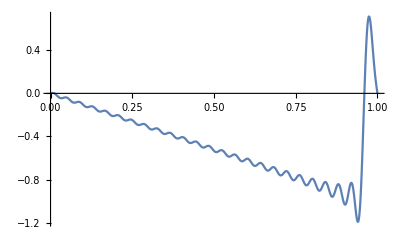

```mathematica
aa5=Transpose[{b,a5}];
q5=ListPlot[aa5,Joined->True]
```

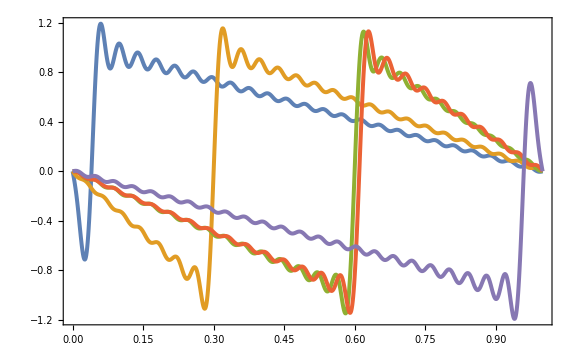

```mathematica
ListPlot[{aa1,aa2,aa3,aa4,aa5},Joined->True,PlotStyle->Thickness[0.005],Frame->{True, True, True, True}]
```